# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\Spin chains\Open XXZ

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Noisy open Heisenberg

## Purities of chaometer

```mathematica
Clear[Noisyheinsenberg];
Noisyheinsenberg[hz_,L_] := Module[{NNindices,a,b},
	NNindices=Normal[SparseArray[Thread[{#,#+1}->1],{L}]&/@Range[L-1]];
	a=N[Normal[Total[Join[(Pauli/@NNindices),(Pauli/@(2NNindices)),(Pauli/@(3NNindices))]]]];
	b=DiagonalMatrix[hz].Normal[Total[(Pauli[3#]&/@IdentityMatrix[L])]];
	a+b
]
```

```mathematica
L=10;
hz=Table[RandomReal[{-0.5,0.5}],{i,2^L}];
H=Noisyheinsenberg[hz,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
iprsvectores=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

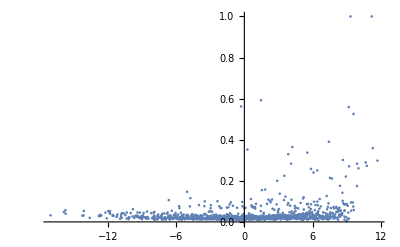

```mathematica
ListPlot[Transpose[{eigenval,iprsvectores}],PlotRange->All]
```

```mathematica
L=5;
hmax=5;
hz=Table[RandomReal[{-hmax,hmax}],{i,2^L}];
H=Noisyheinsenberg[hz,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
blochtest=Table[qubit[i,0],{i,0,Pi,Pi/(ale2-1)}];
```

```mathematica
(*ψTa=coherentstate[qubit[0,0],L-1];*)
ψTa=RandomChainProductState[L-1];
ψa=Table[Flatten[KroneckerProduct[ψTa,i]],{i,blochtest}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
```

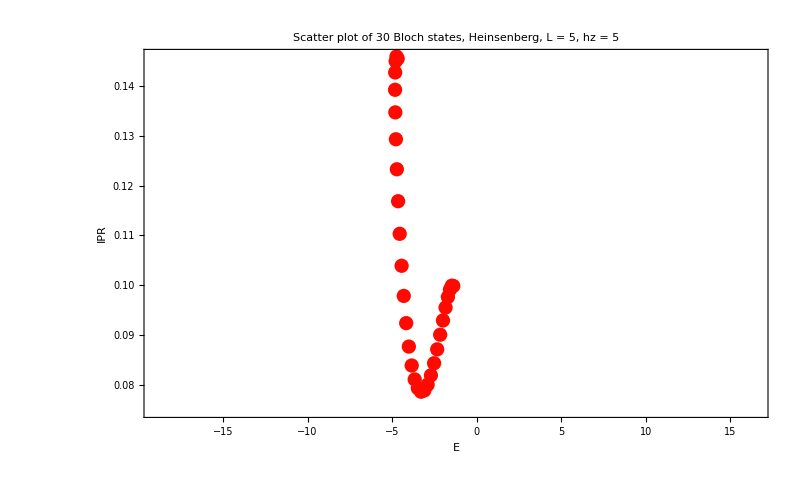

```mathematica
ListPlot[Transpose[{energiesa,iprsa}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" Bloch states, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->coloursc[[1]],PlotRange->{{Min[eigenval],Max[eigenval]},All},ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

```mathematica
tf=20;
dt=0.1;
tlist=Range[0,tf,dt];
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
```

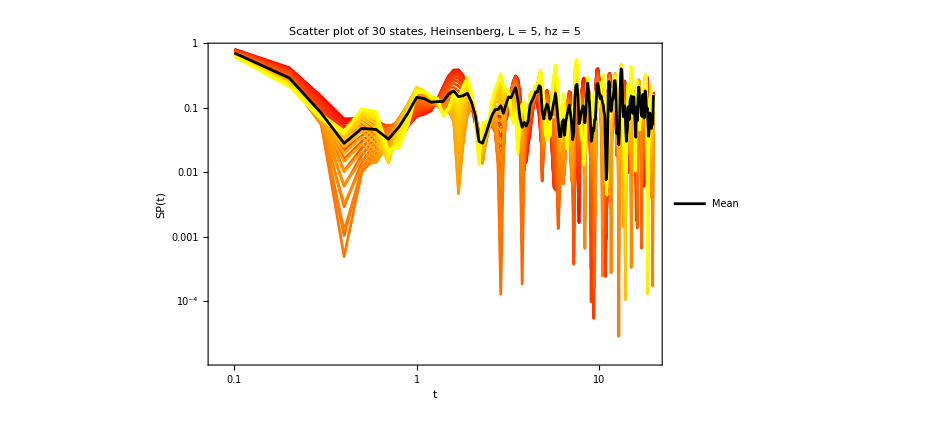

```mathematica
singlea=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->coloursc,PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meana=ListLogLogPlot[Mean[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->{Directive[Black,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
Show[{singlea,meana}]
```

```mathematica
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
data={};
data2={};
Do[
densitya=Table[Dyad[j,j],{j,ψat[[k,All]]}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
AppendTo[data2,reduceda];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
AppendTo[data,puritiesa];
,{k,ale2}];
```

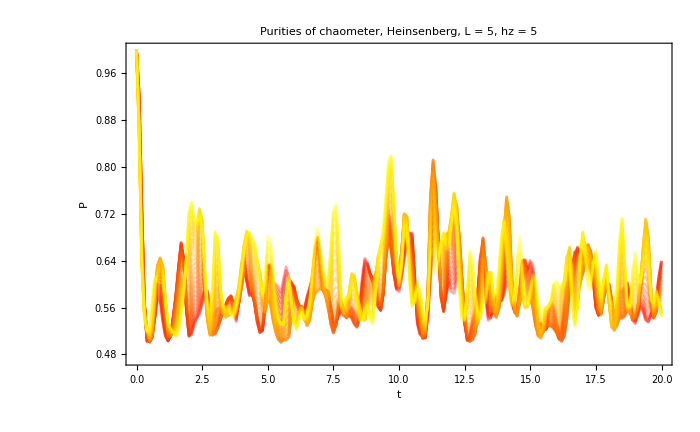

```mathematica
tlist=Range[0,tf,dt];
uno=ListPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of chaometer, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.35]],{j,coloursc}],PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
data2x={};
data2y={};
data2z={};
Do[
reducedmagax=Table[Chop[Tr[sx.i]],{i,data2[[k,All]]}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,data2[[k,All]]}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,data2[[k,All]]}];
AppendTo[data2x,reducedmagax];
AppendTo[data2y,reducedmagay];
AppendTo[data2z,reducedmagaz];
,{k,ale2}];
```

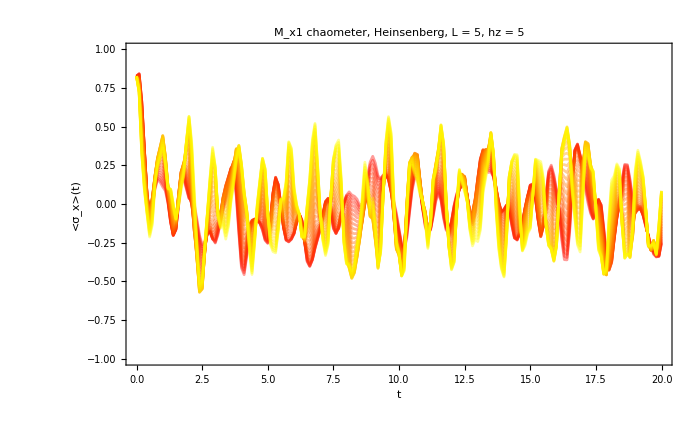

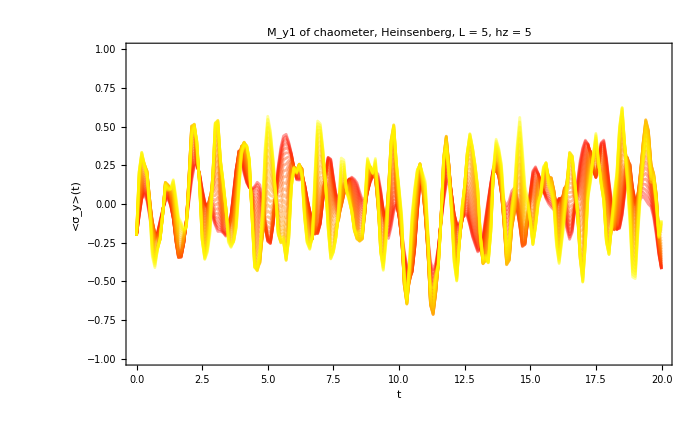

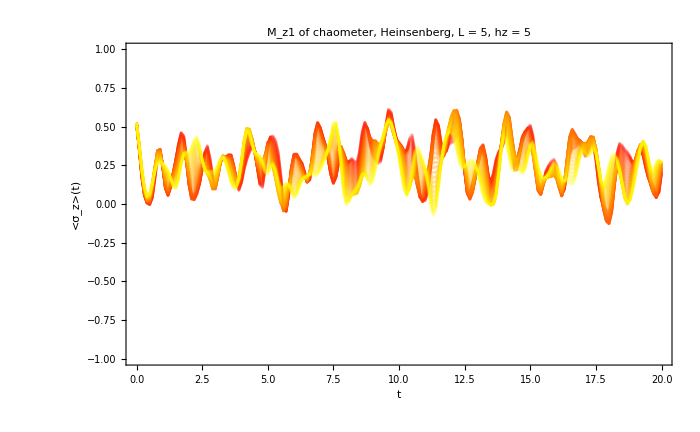

```mathematica
ListPlot[Table[Transpose[{tlist,k}],{k,data2x}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_x1 chaometer, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_x(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_x>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2y}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_y1 of chaometer, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_y(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_y>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2z}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of chaometer, Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_z(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_z>(t)"]}]
```

# Product states characterization

```mathematica
?OpenXXZHamiltonian
```

```mathematica
L=5;
Δ=1.;
H=OpenXXZHamiltonian[L,Δ,0,0];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
ale=200;
caometer=Table[haar[1],{i,ale}];
```

```mathematica
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
(*coloursc=Table[RGBColor[1-i,i/ale2,1-i],{i,ale2}];*)
single=qubit[0,0];
blochtest=Table[qubit[i,0],{i,0,Pi,Pi/ale2}];
```

```mathematica
scatterplots={};
scatterplots2c={};
ψec={};

Do[

(*ψTc=Flatten[KroneckerProduct[coherentstate[single,L-2],N[blochtest[[i]]]]];*)
ψTc=RandomChainProductState[L-1];
(*ψTc=haar[L-1];*)
AppendTo[ψec,ψTc];
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];

scatter1=ListPlot[Transpose[{energiesc,iprsc}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Open XXZ, L = "<>ToString[L]<>", hz = "<>ToString[Δ]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.25]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}];
AppendTo[scatterplots,scatter1];

iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
scatter2c=ListPlot[{Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Open XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
AppendTo[scatterplots2c,scatter2c];

,{i,ale2}];
```

```mathematica
Show[scatterplots,PlotRange->All];
Show[scatterplots2c,PlotRange->All];
```

## Quantum channel

```mathematica
tf=20;
dt=0.1;
(*QUANTUM CHANNEL*)
ψe=ψec;
styles={Style["Product state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};
spectrum={};

Do[

choiEigenvalues={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[spectrum,Eigenvalues[superOp]];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,dt}];

AppendTo[allchoieigenvalues,
Chop[choiEigenvalues]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];
```

```mathematica
limit=Plot[{0.5,0.25},{x,0,tf},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
enerpury=Plot[{energyentropy},{x,0,tf},PlotStyle->Directive[Brown,Opacity[0.05]]];
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.5]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];
```

```mathematica
plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];
```

```mathematica
testimage=Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],Show[{spectrumplots[[1]],spectrumplots[[16]],spectrumplots[[-1]]}]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["frame_randomproducstate_openxxz_L_"<>ToString[L]<>"_Δ_"<>ToString[Δ]<>"_tf_"<>ToString[tf]<>".png",testimage];
```

## spectrum

```mathematica
tlist=Range[0,tf,dt];
newspectrum=ArrayReshape[spectrum,{ale2,Length[tlist],4}];
spectrumplots=Table[ComplexListPlot[newspectrum[[i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[i]],PlotLabel->Style["Spectrum plot of Heinsenberg, L = "<>ToString[L]<>", hz = "<>ToString[hmax]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[newspectrum]}];
```

```mathematica
Table[Export["spectrum_Heinsenberg_randomproductstate_L_"<>ToString[L]<>"_hz_"<>ToString[hmax]<>"_tf_"<>ToString[tf]<>"_enviroment_end_"<>ToString[i]<>".png",spectrumplots[[i]]],{i,ale2}]
```

```mathematica
Export["spectrum_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_tf_"<>ToString[tf]<>".mp4",spectrumplots,"FrameRate"->1]
```

```mathematica
tlist=Range[0,tf,dt];
newspectrum=spectrum[[1;;Length[tlist]]];
```

```mathematica
spectrumplots3=Table[ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[tlist]}];
```

```mathematica
Export["spectrum_heinsenberg_excitation_lastsite_blochtest_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_tf_"<>ToString[tf]<>".mp4",spectrumplots3,"FrameRate"->10]
```

$Aborted

## Different size spectrums

```mathematica
spectrumplots=Table[Grid[{{spectrumplots3[[i]],spectrumplots4[[i]]},{spectrumplots5[[i]],spectrumplots6[[i]]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All],{i,Length[tlist]}];
```

```mathematica
Table[Export["spectrum_L_3456_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_"<>ToString[i]<>".png",spectrumplots[[i]]],{i,Length[spectrumplots]}]
```

```mathematica
Export["spectrum_L_3456_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".mp4",spectrumplots,"FrameRate"->10]
```

Export::interr2: An unknown internal error occurred. Consult Internal`$LastInternalFailure for potential information.

$Failed

## Plotting as a function of t

```mathematica
tlist=Range[0,tf,dt];
newspectrum=spectrum[[1;;Length[tlist]]];
```

```mathematica
spectrumplots=Table[ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,100}];
```

```mathematica
spectrumplots=Table[Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All],{i,Length[tlist]}];
```

```mathematica
Export["spectrum_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".mp4",spectrumplots,"FrameRate"->10]
```

spectrum_L_5_hz_0.5.mp4

```mathematica
ListAnimate[spectrumplots,AnimationRunning->False]
```

## SP(t)

```mathematica
ψec//Dimensions
```

{10,64}

```mathematica
newψec=Table[Flatten[KroneckerProduct[haar[1],i]],{i,ψec}];
```

```mathematica
tlist=Range[0,tf,0.1];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,newψec},{t,0,tf,0.1}];
```

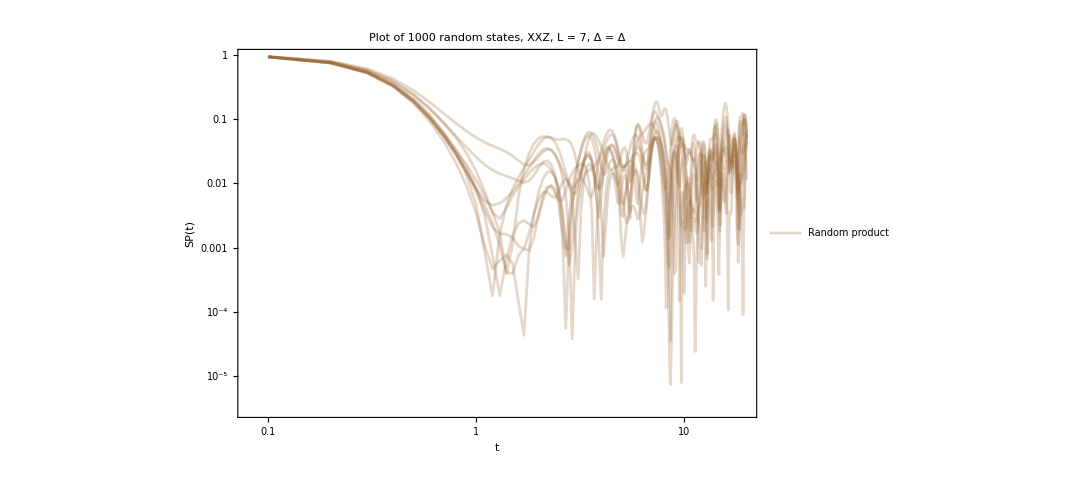

```mathematica
singlec=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2},{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown,Opacity[0.25]]},PlotRange->All,ImageSize->800,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

# Sweep hz

```mathematica
ale=2000;
caometer=Table[haar[1],{i,ale}];
ale2=10;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
single=qubit[0,0];
tf=15.;
dt=0.025;
L=5;
hx=J=1.;
```

```mathematica
Do[

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];

scatterplots={};
scatterplots2c={};
ψec={};

Do[
ψTc=Flatten[KroneckerProduct[coherentstate[single,L-2],haar[1]]];
AppendTo[ψec,ψTc];
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
scatter1=ListPlot[Transpose[{energiesc,iprsc}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.25]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}];
AppendTo[scatterplots,scatter1];
iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
scatter2c=ListPlot[{Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
AppendTo[scatterplots2c,scatter2c];
,{i,ale2}];
Show[scatterplots,PlotRange->All];
Show[scatterplots2c,PlotRange->All];

(*QUANTUM CHANNEL*)
ψe=ψec;
styles={Style["Random product state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};
(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};
spectrum={};

Do[

choiEigenvalues={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[spectrum,Eigenvalues[superOp]];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,dt}];

AppendTo[allchoieigenvalues,
Chop[choiEigenvalues]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];

limit=Plot[0.25,{x,0,tf},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.5]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];

plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

tlist=Range[0,tf,dt];
newspectrum=ArrayReshape[spectrum,{10,Length[tlist],4}];
spectrumplots=Table[ComplexListPlot[newspectrum[[i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[i]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[newspectrum]}];
testimage=Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],spectrumplots[[1]]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["frame_wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_zeroenviroment_excitationatend_"<>ToString[ale2]<>"_.png",testimage,ImageResolution->300];


,{hz,0,3,0.01}]
```

$Aborted